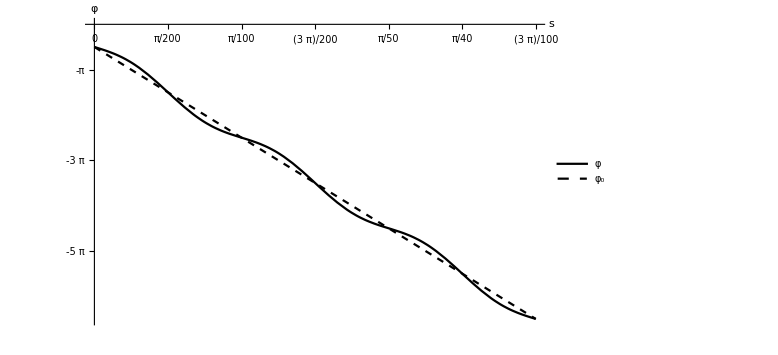

```mathematica
l=10^-2;
α=1/( l );

opts={Ticks->{Range[0,3Pi l,Pi l/2],Range[Pi,-10Pi,-Pi]},AxesLabel->{"
StyleBox[\"s\",\nFontSlant->\"Italic\"]","φ"},PlotStyle->{Black,{Black,Dashed}},ImageSize->Large,PlotLegends->{Text[Style["φ",16]],Text[Style["φ_0",16]]},AxesStyle->15};
fminus[s_]:=-2 s/l-π/2+α l Sin[2 s/l]/2 
plt = Plot[{fminus[s],-2 s/l-π/2},{s,0, 3 Pi l},Evaluate[opts]]
```

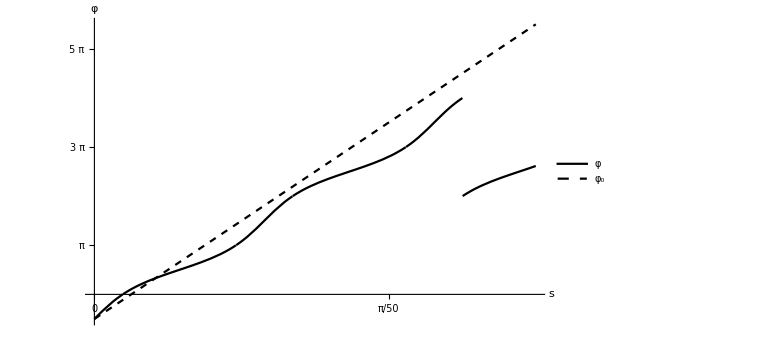

```mathematica
s0=l ArcTan[(1+α l/2)/Sqrt[1-α^2 l^2/4]]/Sqrt[1-α^2 l^2/4];
fteor[s_]:=π+2 ArcTan[Sqrt[1-α^2 l^2/4] Tan[(s+s0)Sqrt[1-α^2 l^2/4]/l]-α l/2]
Plot[{
If[Abs[fteor[s]-2Pi-(2 s/l-π/2)]<Pi/2,
fteor[s]-2Pi,
If[Abs[fteor[s]-(2 s/l-π/2)]<Pi/2,fteor[s],fteor[s]+2Pi]],
2 s/l-π/2},{s,0,3 Pi l},Evaluate[opts]]
```

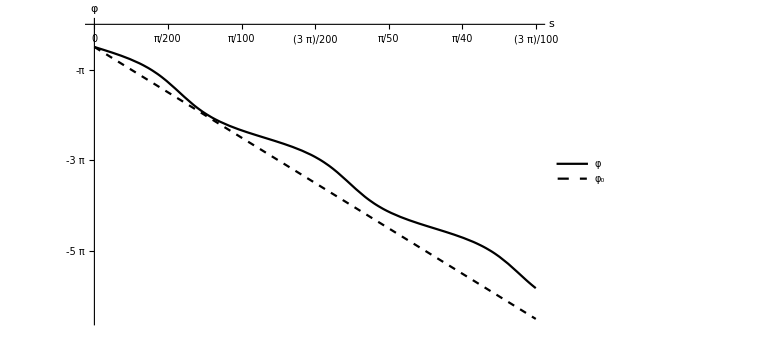

```mathematica
rown=y'[s]+2/l+α Sin[y[s]]==0;
sol=NDSolve[{rown,y[0]==-Pi/2},y[s],{s,0,10Pi l}];
(*opts1={Ticks->{Range[0,Pi/10,Pi/50],Range[-Pi,20Pi,5Pi]},AxesLabel->{"s","φ"},PlotStyle->{Black,{Black,Dashed}},ImageSize->Large,PlotLegends->{"φ","φ_0"}};*)
plt=Plot[{y[s]/.sol,-2 s/l-π/2},{s,0, 3Pi l},Evaluate[opts]]
```

```mathematica
Export["HiperAppA100L2M.eps",plt]
```

HiperAppA100L2M.eps